```mathematica
(*GLOBAL INITIALIZATION*)
(*Initialize kernals*)
ParallelEvaluate[$RecursionLimit=100000];
kernalIDs=ParallelEvaluate[$KernelID]

(*Position of the lost plan*)
distantR = 0.8;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
θ=RandomReal[{0,2π}];
lostX = distantR*Cos[θ];
lostY = distantR*Sin[θ];
(*stepDist is the *)
stepDist=0.1;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
rangeX={-1,1};
rangeY={-1,1};
(*Minimal Probability possible*)
(*minP=1/((rangeX[[2]]-rangeX[[1]])*((rangeY[[2]]-rangeY[[1]]))/stepDist^2*10000);*)
minP=0;
(*Function that change from a position to an index*)
indexOf[x_,y_]:=Module[{},
{Round[(x-(rangeX[[1]]))/stepDist]+1,Round[(y-(rangeY[[1]]))/stepDist]+1}
];
lostIndexP=indexOf[lostX,lostY];
lostIndexX=lostIndexP[[1]];
lostIndexY=lostIndexP[[2]];

(*Whether to show the update when the searcher is searching something*)
displayDuringSearching=False;
```

{1,2,3,4}

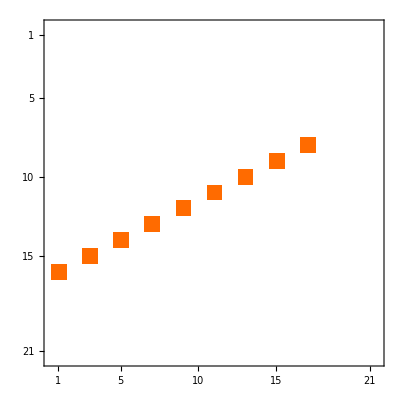
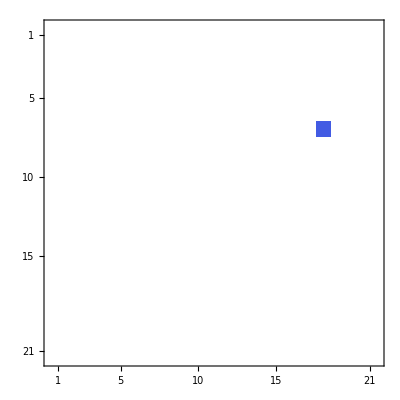
{-Graphics-,-Graphics-,{-0.361768,0.713529}}

```mathematica
(*Simulation Environment*)
(*If the position(x,y) is on the path*)
isOnPath[x_,y_]:=Module[{m=lostY/lostX, expT=prec},
(*Linear Path*)
Abs[x-0]+Abs[x-Cos[ArcTan[m]]*distantR]-1<expT && 
Abs[y-m*x] <expT
];

(*Whether the position is the plane position*)
isFound[x_,y_]:=Module[{rt = prec,lp,lx,ly},
lp=indexOf[x,y];
lx=lp[[1]];
ly=lp[[2]];
lostIndexX==lx && lostIndexY==ly
];

(* The probability that we give evidence when searching at the path*)
pEvidenceFoundOnPath=0.3;

(*Search a particular Point in the map*)
searchMapAtPoint[x_,y_]:=Module[{p=RandomReal[{0,1}] < pEvidenceFoundOnPath},
isOnPath[x,y] && p
];

(*Update the Data At Specific Point*)
changeDataAt[list_,posX_,posY_,newValue_]:=Parallelize[Table[
If[
Abs[posX-x]< prec &&Abs[posY-y]<prec,
newValue,
list[[
indexOf[x,y][[1]]
]][[
indexOf[x,y][[2]]
]]
],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]
];

(*Initialize experiment Environment*)
generateLostPoint[r_,theta_,step_,range_]:=Module[{},
(*Position of the lost plan*)
distantR = r;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
θ=theta;
{lostX,lostY}={distantR*Cos[θ],distantR*Sin[θ]};

{lostIndexX,lostIndexY}=lostIndexP=indexOf[lostX,lostY];

(*stepDist is the *)
stepDist=step;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
{rangeX,rangeY}=range;
];

plotPlaneInformation[]:=Module[{},
(*Plot lost point*)
planePathData = Parallelize[Table[If[isOnPath[x,y],1,0],{x,-1,1,stepDist},{y,-1,1,stepDist}]];
plotLostPlane =Parallelize[Table[0,{x,-1,1,stepDist},{y,-1,1,stepDist}]];
plotLostPlane= changeDataAt[plotLostPlane,lostX,lostY,-100];

Print[{
(*ListDensityPlot[planePathData,PlotRange->All],
ListDensityPlot[data,PlotRange->All],*)
MatrixPlot[planePathData,PlotRange->All],
MatrixPlot[plotLostPlane,PlotRange->All],
{lostX,lostY}
}];
];
plotPlaneInformation[];
```

```mathematica
(* 
  searcher data is the probability density of the 
	probability that the searcher can find the object
	given that the object is in the position
	P(D|O)
data is the probability density of the 
	probability that if the object is in the position
	and given that we can detected it
	P(D|O)*P(O)=P(O|D)
*)
searcherModel[objectData_,searcherData_]:=Module[{
data,

getSearchPoint,
searchPoint,
plotData,
max=-Infinity,
x=rangeX[[1]], y=rangeY[[1]],
mx=0,my=0,ix,iy
},

data=objectData*searcherData;

(* Found the next search point *)
While[x-rangeX[[2]] < prec,
While[y-rangeY[[2]] < prec,
{ix,iy}=indexOf[x,y];
If[
max<data[[ix]][[iy]],
max=data[[ix]][[iy]];
mx=x;
my=y;
(*Print[{max,list[[ix]][[iy]], {ix,iy},{x,y},{px,py}}]*);
];
y+=stepDist;
];
y=rangeY[[1]];
x+=stepDist;
];

searchPoint ={mx,my};
(*plotData= changeDataAt[data,mx,my,-1];*)
If[displayDuringSearching,
Print[{MatrixPlot[data],MatrixPlot[objectData],MatrixPlot[searcherData],MatrixPlot[plotData]}];
Print[{
ListPointPlot3D[data,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[objectData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[searcherData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
(*ListPlot3D[plotData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[z]]]*)
}
];
];

Return[
<|
ret->Apply[isFound,searchPoint],
pos->searchPoint,
posIndex->Apply[indexOf,searchPoint],
pdo-> searcherData[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]],
poo-> data[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]]
|>
];
];
```

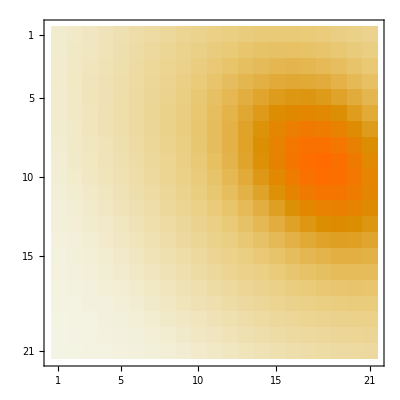
{-Graphics3D-,-Graphics-}

```mathematica
(* Object Data *)
(* precondition:  0<ρ<1 *)
objectDataInit[ρ_:0.3,σx_:0.3,σy_:0.3,γ_:0.2]:=Module[{centerX,centerY},
centerX=lostX*0.8+γ*RandomReal[]*distantR;
 centerY=lostY*0.8+γ*RandomReal[]*distantR;
Function[{x,y},PDF[MultinormalDistribution[{centerX,centerY},{{σx^2,ρ*σx*σy},{ρ*σx*σy,σy^2}}],{x,y}]*stepDist^2]
];

(*Update ObjectData*)
updateObjectData[f_]:=Module[{},
objectData=Parallelize[
Table[f[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]]
];

(* has to manually initialize *)
tmpf=objectDataInit[];
updateObjectData[tmpf];

Print[{
DiscretePlot3D[tmpf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[objectData]
}];
```

```mathematica
(*FUnction that display data pdf*)
printDataPDF[pdf_]:=Module[{tmp},
tmp=Parallelize[Table[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}]];
Print[{
DiscretePlot3D[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[tmp],
(*tmp*)
}];
];
```

```mathematica
(* {cx,cy} is the initial center of the searcher *)
(* precondition:  0<ρ<1 *)
generateSearcherData[centerX_,centerY_,a_,bx_,by_]:=Module[
{},
Function[{x,y},PDF[MultinormalDistribution[{centerX,centerY},{{bx^2,a*bx*by},{a*bx*by,by^2}}],{x,y}]*stepDist^2*50]
];

searchers={};

(* 
Generate Searchers of a specific functions for multiple times(allowed different configurations);
	para;
		num=>number of searchesr;
		fun: function of the pdf*area;
		parameters: a list of parameters for each function, could be the same or different
*)
generateSearchers[funs_]:=Module[{},
searchers= Parallelize[Map[
Function[f,Table[
f[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]],funs]
]
];

initSearcherFunctions[maxT_]:=Module[{initList={},i},
For[i=0,i<maxT,i++,initList=Append[initList,1]];
Parallelize[Map[Function[para,Apply[generateSearcherData,para]],
Map[Function[a,Map[Function[x,RandomReal[x]],{{-1,1},{-1,1},{-1,1},{0,1},{0,1}}]],initList]
]]
];
generateSearchers[initSearcherFunctions[5]];
```

```mathematica
(* Let a list of searchers to search with a particular condition *)
allSearch[searchers_,objectData_]:=
WaitAll[ParallelSubmit[Map[Function[sd,searcherModel[objectData,sd]],searchers]]];

(*searchResults=allSearch[searchers,objectData];*)
```

```mathematica
(* Incorproate the search result to generate a new update*)

(* test whether the search is successful *)
isSuccessful[result_]:=Fold[Or,False,Parallelize[Map[Function[a,a[ret]],result]]];
```

```mathematica
(*Flatter the list so that I know what are the position that the searcher searched*)
restracture[result_]:=
Parallelize[Map[Function[a,{a[posIndex],a[poo]*a[pdo],a[poo]*(1-a[pdo])}],result]];
```

```mathematica
calculateDenominator[restruct_]:=Fold[Function[{x,y},x-y],1,restruct][[2]];
```

```mathematica
reduceColumneProduct[restruct_,denominator_]:=Parallelize[Map[Function[x,{x[[1]],x[[3]]/denominator}],restruct]];
```

```mathematica
(* Function to check whether contains *)
restructContains[result_,{px_,py_}]:=Fold[
Function[{prev,current},
prev || current[[1]] == {px,py}
],False,result];
```

```mathematica
(*
Extract result from the structure 
TODO! should I make it return ZERO? which is safer?
*)
extractRestruct[result_,{px_,py_}]:=
Fold[Function[{prev,current},
If[prev==-Infinity &&current[[1]] == {px,py},current[[2]],prev]
],-Infinity,result];
```

```mathematica
(* Generate a new List *)
updateObjectProbabilityAfterFail[result_,denominator_,originalObjectData_ ]:=Module[{tmp,f},
f[x_,y_]:=Module[{pos},
pos=indexOf[x,y];
If[
restructContains[result,pos],
extractRestruct[result,pos],
originalObjectData[[pos[[1]]]][[pos[[2]]]]/denominator
 ]
];
Parallelize[Table[f[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}]]
];
```

```mathematica
(*Main Searcher Algorithm*)
(*
	1. po(plot);
	2. search plot;
	3. pd=po*pdo sum
*)
multiSearcherSearch[initObjectData_,searchers_,max_]:=Module[
{data=initObjectData,searchResults,temp,originalData,restruct,denominator,restructSearchRet,t,diff=initObjectData},
Print["Search Begin!"];
Monitor[
t=0;
While[t==0||!isSuccessful[searchResults] && t<max,
originalData=data;
(*Print[MatrixPlot[originalData]];*)

(*get the search result*)
searchResults=allSearch[searchers,originalData];
(*Print[MatrixForm[searchResults]];*)

restructSearchRet=restracture[searchResults];
(*Print[restructSearchRet];*)

denominator=calculateDenominator[restructSearchRet];
(*Print[denominator];*)

restruct=reduceColumneProduct[restructSearchRet,denominator];
(*Print[restruct];*)

data=updateObjectProbabilityAfterFail[restruct,denominator, originalData];
diff =originalData-data;
(*NotebookDelete[temp];
temp=PrintTemporary[{MatrixPlot[originalData],MatrixPlot[data],MatrixPlot[originalData-data],t}];*)
t++;
];
,{MatrixPlot[originalData],MatrixPlot[data],MatrixPlot[diff],t}];

Print[{MatrixPlot[initObjectData],MatrixPlot[data], MatrixPlot[initObjectData-data],t}];Print[{ListPlot3D[initObjectData,PlotRange->All], ListPlot3D[data,PlotRange->All],ListPlot3D[initObjectData-data,PlotRange->All]}];
Print[MatrixForm[searchResults]];
];
```

```mathematica
(*
1. generate your P(O) distribution,each will be a function to plug into updateObjectData[f]
original function will be object data init, which is a binoral distribution centered at the place where the plane is lost
*)
(*updateObjectData[objectDataInit];*)

(*
2. generate your searchers!(each one is a PDF that can be put into≥
*)

(*multiSearcherSearch[objectData,searchers,50]*)
```

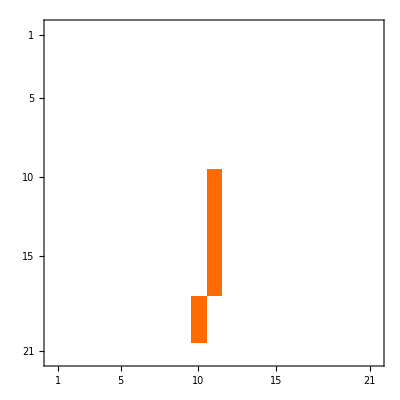
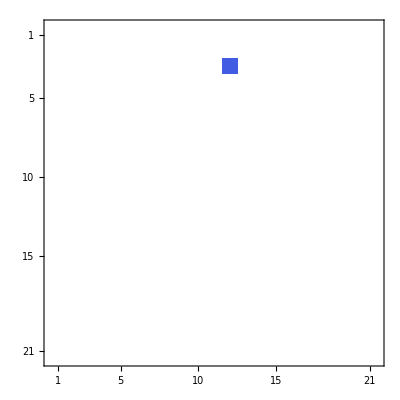
{-Graphics-,-Graphics-,{-0.797445,0.0638879}}

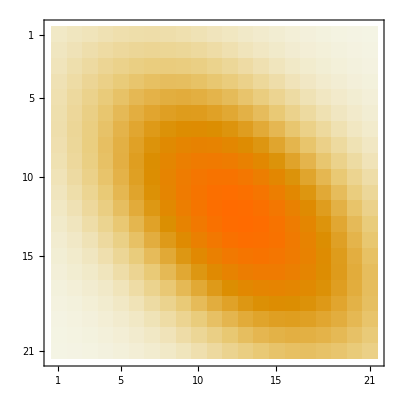
{-Graphics-,-Graphics3D-}

$Aborted

```mathematica
(*
	1. Single searcher;
	2. 20*20= 400 areas; step=0.05
	3. PO = multinormal distribution;
	3. PDO = bimodal multivariable possoin distribution
*)
SimulationOne[]:=Module[{searchers,objectData,pdo,𝒟,f,prod},
(*initialize the environment*)
generateLostPoint[0.8,RandomReal[{0,π}],0.1,{{-1,1},{-1,1}}];
plotPlaneInformation[];

f=objectDataInit[0.5,0.5,0.5];
objectData=updateObjectData[f];
Print[{MatrixPlot[objectData],ListPlot3D[objectData,PlotRange->All]}];

𝒟=MixtureDistribution[{3,1},{MultivariatePoissonDistribution[7,{9,10}],MultivariatePoissonDistribution[2,{5,4}]}];
searchers={ParallelTable[100*PDF[𝒟,{x,y}],
{x,5,25},
{y,5,25}
]};
Print[{MatrixPlot[searchers[[1]]], ListPlot3D[searchers[[1]],PlotRange-> All]}];

Print[{MatrixPlot[searchers[[1]]*objectData], ListPlot3D[searchers[[1]]*objectData,PlotRange-> All]}];

multiSearcherSearch[objectData,searchers,Infinity];
];
SimulationOne[];
```